Physical parameters: λ is the coupling parameter, i.e. the frequency difference between the bare mechanical (angular) frequency and the shifted ones (the difference between the fast and the slow frequencies is thus 2λ); Ω is the angular mechanical frequency (2πf); Nth is the number of thermal phonons of the bath; Q is the quality factor; T2 is T2; B is the amplitude of the cantilever motion in natural units; Nimp is excitation number associated with the initial uncertainty of the position of the cantilever (which I assumed here to be the measurement imprecision noise); nc is the number of cycles

Just fill the physical parameters in and run

```mathematica
λ=2π*0.045;
Ω=2π*3000; 
Nth=0;
Q=100000;
T2=0.1;
B=100000;
Nimp=760;
nc=5;
δ=Sqrt[0.5*(Nimp+0.5)];

τ=(2π*nc)/Ω;
γ=Ω/(2π*Q);
ξ=Sqrt[γ^2-4*λ^2+8I*γ*λ*(Nth+0.5)];
hM=(-γ+ξ)/(2γ(Nth+0.5)+I*λ);hm=(-γ-ξ)/(2γ(Nth+0.5)+I*λ);
```

```mathematica
(* Most of what follows is just the construction of the final function;You can skip it until the mark;This was constructed to make it easier for me to have the final function running and to check if the intermediate steps made sense. *)
```

This part here is just to check if the input parameters obey the conditions to observe the asymmetry or not. It is not necessary to run this. It was meant just for me to get a feeling of what should we look for

```mathematica
λ*τ*B
```

```mathematica
δ
```

```mathematica
h=Re[P[-Sin[λ*τ]*B]]/Re[P[Sin[λ*τ]*B]]
```

0.999997

```mathematica
nc*Nth/Q
```

0

```mathematica
nc*Nth/Q*(2π*nc*B*λ)/Ω
```

0.

Functions for the time-evolution; essentially the expressions 3.63 to 3.708 from my thesis;

```mathematica
(*'u' and 'd' refer to the 'up' and 'down' spin states*)
```

```mathematica
Dif[t_,g0_]:=g0*(Nth+0.5)*(Exp[-γ*t]-1)+Exp[-γ*t];
DDif[t_,g0_]:=(g0*(Exp[-ξ*t]-1)+hM-hm*Exp[-ξ*t])/(hM-hm);
guu[t_,g0_]:=g0/Dif[t,g0];
kuu[t_,g0_,k0_]:=(k0*Exp[-0.5*γ*t+ⅈ*(Ω+λ)*t])/Dif[t,g0];
quu[t_,g0_,q0_]:=(q0*Exp[-0.5*γ*t-ⅈ*(Ω+λ)*t])/Dif[t,g0];
cuu[t_,g0_,q0_,k0_,c0_]:=c0-Log[Dif[t,g0]]+(q0*k0*(Nth+0.5)*(1-Exp[-γ*t]))/Dif[t,g0];
kdd[t_,g0_,k0_]:=(k0*Exp[-0.5*γ*t+ⅈ*(Ω-λ)*t])/Dif[t,g0];
qdd[t_,g0_,q0_]:=(q0*Exp[-0.5*γ*t-ⅈ*(Ω-λ)*t])/Dif[t,g0];
gud[t_,g0_]:=(g0*(hM*Exp[-ξ*t]-hm)+hM*hm*(1-Exp[-ξ*t]))/((hM-hm)*DDif[t,g0]);
kud[t_,g0_,k0_]:=(k0*Exp[-0.5*ξ*t+ⅈ*Ω*t])/DDif[t,g0];
qud[t_,g0_,q0_]:=(q0*Exp[-0.5*ξ*t-ⅈ*Ω*t])/DDif[t,g0];
cud[t_,g0_,q0_,k0_,c0_]:=c0-Log[DDif[t,g0]]+(q0*k0*(1-Exp[-ξ*t]))/((hM-hm)*DDif[t,g0])+(ⅈ*λ+(γ-ξ)/2-1/T2)*t;

(*Wigner functions and the probability distributions*)

Wuu[x_,p_,t_,g0_,k0_,q0_,c0_]:=Exp[guu[t,g0](x^2+p^2)+kuu[t,g0,k0]*(x+ⅈ*p)+quu[t,g0,q0]*(x-ⅈ*p)+cuu[t,g0,q0,k0,c0]];


Wdd[x_,p_,t_,g0_,k0_,q0_,c0_]:=Exp[guu[t,g0](x^2+p^2)+kdd[t,g0,k0]*(x+ⅈ*p)+qdd[t,g0,q0]*(x-ⅈ*p)+cuu[t,g0,q0,k0,c0]];


Wud[x_,p_,t_,g0_,k0_,q0_,c0_]:=Exp[gud[t,g0](x^2+p^2)+kud[t,g0,k0]*(x+ⅈ*p)+qud[t,g0,q0]*(x-ⅈ*p)+cud[t,g0,q0,k0,c0]];


PPuu[x_,t_,g0_,k0_,q0_,c0_]:=√(π/(-guu[t,g0]))*1/Dif[t,g0]*Exp[guu[t,g0]*(x+((k0*Exp[ⅈ*(Ω+λ)*t]+q0*Exp[-ⅈ*(Ω+λ)*t])*Exp[-0.5*γ*t])/(2*g0))^2+c0-(k0*q0)/g0];


PPdd[x_,t_,g0_,k0_,q0_,c0_]:=√(π/(-guu[t,g0]))*1/Dif[t,g0]*Exp[guu[t,g0]*(x+((k0*Exp[ⅈ*(Ω-λ)*t]+q0*Exp[-ⅈ*(Ω-λ)*t])*Exp[-0.5*γ*t])/(2*g0))^2+c0-(k0*q0)/g0];
```

Evolution after the creation of the superposition

```mathematica
(*Initial conditions*)
```

```mathematica
g0=-1/(2*δ^2);k0=-ⅈ*B/(2*δ^2);q0=Conjugate[ⅈ*B/(2*δ^2)];c0=-B^2/(2*δ^2)-Log[4π*δ^2];
```

```mathematica
(*Wigner functions at t=tau*)
```

```mathematica
Wuu[x,p,τ,g0,k0,q0,c0]
```

ⅇ^((-1.31557×10^7+0. ⅈ)-(0.0619354+131.431 ⅈ) (-ⅈ p+x)+(0.0619354-131.431 ⅈ) (ⅈ p+x)-0.00131434 (p^2+x^2))

```mathematica
Wdd[x,p,τ,g0,k0,q0,c0]
```

ⅇ^((-1.31557×10^7+0. ⅈ)+(0.0619354-131.431 ⅈ) (-ⅈ p+x)-(0.0619354+131.431 ⅈ) (ⅈ p+x)-0.00131434 (p^2+x^2))

```mathematica
Wud[x,p,τ,g0,k0,q0,c0]
```

ⅇ^((-1.31557×10^7-3.30647 ⅈ)-(0.0232608+131.431 ⅈ) (-ⅈ p+x)-(0.0232608+131.431 ⅈ) (ⅈ p+x)-(0.00131445+0.000942037 ⅈ) (p^2+x^2))

```mathematica
(*Gluing of the new initial conditions; the functions below give the coefficients at t=2tau after the pulse at t=tau*)

GUU=guu[τ,-1/(2*δ^2)];
KUU=kuu[τ,-1/(2*δ^2),-ⅈ*B/(2*δ^2)];
QUU=quu[τ,-1/(2*δ^2),ⅈ*B/(2*δ^2)];
CUU=cuu[τ,-1/(2*δ^2),ⅈ*B/(2*δ^2),-ⅈ*B/(2*δ^2),-B^2/(2*δ^2)-Log[4π*δ^2]];
KDD=kdd[τ,-1/(2*δ^2),-ⅈ*B/(2*δ^2)];
QDD=qdd[τ,-1/(2*δ^2),ⅈ*B/(2*δ^2)];
GUD=gud[τ,-1/(2*δ^2)];
KUD=kud[τ,-1/(2*δ^2),-ⅈ*B/(2*δ^2)];
QUD=qud[τ,-1/(2*δ^2),ⅈ*B/(2*δ^2)];
CUD=cud[τ,-1/(2*δ^2),ⅈ*B/(2*δ^2),-ⅈ*B/(2*δ^2),-B^2/(2*δ^2)-Log[-ⅈ*4π*δ^2]];
```

Wuu after the pulse and at t=2τ

```mathematica
0.5*(Wuu[x,p,τ,GUU,KUU,QUU,CUU]+Wuu[x,p,τ,GUU ,KDD,QDD,CUU]+ⅈ*Wuu[x,p,τ, GUD,KUD,QUD,CUD]-ⅈ*Wuu[x,p,τ,Conjugate[GUD] ,Conjugate[KUD],Conjugate[QUD],Conjugate[CUD]])
```

0.5 (ⅈ ⅇ^((-1.31363×10^7+0.299001 ⅈ)+(0.131546+131.369 ⅈ) (-ⅈ p+x)-(0.00773293+131.369 ⅈ) (ⅈ p+x)-(0.0013142+0.000941155 ⅈ) (p^2+x^2))-ⅈ ⅇ^((-1.31363×10^7-0.299001 ⅈ)+(0.00773293-131.369 ⅈ) (-ⅈ p+x)-(0.131546-131.369 ⅈ) (ⅈ p+x)-(0.0013142-0.000941155 ⅈ) (p^2+x^2))+ⅇ^((-1.31363×10^7+0. ⅈ)+(1.44952×10^-13+131.369 ⅈ) (-ⅈ p+x)+(1.44952×10^-13-131.369 ⅈ) (ⅈ p+x)-0.00131376 (p^2+x^2))+ⅇ^((-1.31363×10^7+0. ⅈ)+(0.123813+131.369 ⅈ) (-ⅈ p+x)+(0.123813-131.369 ⅈ) (ⅈ p+x)-0.00131376 (p^2+x^2)))

Wdd after the pulse and at t = 2τ

```mathematica
0.5*(Wdd[x,p,τ,GUU ,KUU,QUU,CUU]+Wdd[x,p,τ,GUU,KDD,QDD,CUU]-ⅈ*Wdd[x,p,τ,GUD ,KUD,QUD,CUD]+ⅈ*Wdd[x,p,τ,Conjugate[GUD] ,Conjugate[KUD],Conjugate[QUD],Conjugate[CUD]])
```

0.5 (-ⅈ ⅇ^((-1.31363×10^7+0.299001 ⅈ)+(0.00773293+131.369 ⅈ) (-ⅈ p+x)-(0.131546+131.369 ⅈ) (ⅈ p+x)-(0.0013142+0.000941155 ⅈ) (p^2+x^2))+ⅈ ⅇ^((-1.31363×10^7-0.299001 ⅈ)+(0.131546-131.369 ⅈ) (-ⅈ p+x)-(0.00773293-131.369 ⅈ) (ⅈ p+x)-(0.0013142-0.000941155 ⅈ) (p^2+x^2))+ⅇ^((-1.31363×10^7+0. ⅈ)-(0.123813-131.369 ⅈ) (-ⅈ p+x)-(0.123813+131.369 ⅈ) (ⅈ p+x)-0.00131376 (p^2+x^2))+ⅇ^((-1.31363×10^7+0. ⅈ)+(1.44952×10^-13+131.369 ⅈ) (-ⅈ p+x)+(1.44952×10^-13-131.369 ⅈ) (ⅈ p+x)-0.00131376 (p^2+x^2)))

Wud after the pulse and at t = 2 τ

```mathematica
0.5*(ⅈ*Wud[x,p,τ,GUU ,KUU,QUU,CUU]-ⅈ*Wud[x,p,τ,GUU ,KDD,QDD,CUU]+Wud[x,p,τ,GUD ,KUD,QUD,CUD]+Wud[x,p,τ,Conjugate[GUD] ,Conjugate[KUD],Conjugate[QUD],Conjugate[CUD]])
```

0.5 (ⅇ^((-1.31363×10^7+3.60296 ⅈ)+(0.0928892+131.369 ⅈ) (-ⅈ p+x)-(0.0928892+131.369 ⅈ) (ⅈ p+x)-(0.00131465+0.00188319 ⅈ) (p^2+x^2))+ⅇ^((-1.31363×10^7+3.00496 ⅈ)+(0.0463894-131.369 ⅈ) (-ⅈ p+x)-(0.0463894-131.369 ⅈ) (ⅈ p+x)-(0.00131398+8.81245×10^-7 ⅈ) (p^2+x^2))-ⅈ ⅇ^((-1.31363×10^7+3.30396 ⅈ)-(0.0386565-131.369 ⅈ) (-ⅈ p+x)-(0.0851563+131.369 ⅈ) (ⅈ p+x)-(0.00131387+0.000942037 ⅈ) (p^2+x^2))+ⅈ ⅇ^((-1.31363×10^7+3.30396 ⅈ)+(0.0851563+131.369 ⅈ) (-ⅈ p+x)+(0.0386565-131.369 ⅈ) (ⅈ p+x)-(0.00131387+0.000942037 ⅈ) (p^2+x^2)))

Probability at t=2τ

```mathematica
P2t[x_]:=0.5*(PPuu[x,τ,GUU ,KUU,QUU,CUU]+PPuu[x,τ,GUU ,KDD,QDD,CUU]+ⅈ*PPuu[x,τ,GUD,KUD,QUD,CUD]-ⅈ*PPuu[x,τ,Conjugate[GUD] ,Conjugate[KUD],Conjugate[QUD],Conjugate[CUD]])+0.5*(PPdd[x,τ,GUU ,KUU,QUU,CUU]+PPdd[x,τ,GUU ,KDD,QDD,CUU]-ⅈ*PPdd[x,τ,GUD ,KUD,QUD,CUD]+ⅈ*PPdd[x,τ,Conjugate[GUD] ,Conjugate[KUD],Conjugate[QUD],Conjugate[CUD]])
```

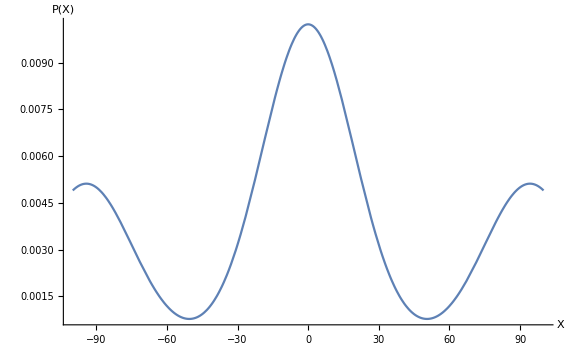

```mathematica
Plot[Re[P2t[x]],{x,-200,200},ImageSize->Large,PlotRange->All,AxesLabel->{"X","P(X)"}]
```

```mathematica
(*   ********************************************************************   *)
(*                                                                          *)
(*                           FINAL PART; RUN THIS                           *)
(*                                                                          *)
(*   ********************************************************************   *)



(*Functions for the time-evolution;essentially the expressions 3.63 to 3.70 from my thesis; the 'u' and 'd' subscripts refer to the 'up' and 'down' spin states of the density matrix *)

Dif[t_,g0_]:=g0*(Nth+0.5)*(Exp[-γ*t]-1)+Exp[-γ*t];
DDif[t_,g0_]:=(g0*(Exp[-ξ*t]-1)+hM-hm*Exp[-ξ*t])/(hM-hm);
guu[t_,g0_]:=g0/Dif[t,g0];
kuu[t_,g0_,k0_]:=(k0*Exp[-0.5*γ*t+ⅈ*(Ω+λ)*t])/Dif[t,g0];
quu[t_,g0_,q0_]:=(q0*Exp[-0.5*γ*t-ⅈ*(Ω+λ)*t])/Dif[t,g0];
cuu[t_,g0_,q0_,k0_,c0_]:=c0-Log[Dif[t,g0]]+(q0*k0*(Nth+0.5)*(1-Exp[-γ*t]))/Dif[t,g0];
kdd[t_,g0_,k0_]:=(k0*Exp[-0.5*γ*t+ⅈ*(Ω-λ)*t])/Dif[t,g0];
qdd[t_,g0_,q0_]:=(q0*Exp[-0.5*γ*t-ⅈ*(Ω-λ)*t])/Dif[t,g0];
gud[t_,g0_]:=(g0*(hM*Exp[-ξ*t]-hm)+hM*hm*(1-Exp[-ξ*t]))/((hM-hm)*DDif[t,g0]);
kud[t_,g0_,k0_]:=(k0*Exp[-0.5*ξ*t+ⅈ*Ω*t])/DDif[t,g0];
qud[t_,g0_,q0_]:=(q0*Exp[-0.5*ξ*t-ⅈ*Ω*t])/DDif[t,g0];
cud[t_,g0_,q0_,k0_,c0_]:=c0-Log[DDif[t,g0]]+(q0*k0*(1-Exp[-ξ*t]))/((hM-hm)*DDif[t,g0])+(ⅈ*λ+(γ-ξ)/2-1/T2)*t;



(*Wigner functions and probability distributions *)

Wuu[x_,p_,t_,g0_,k0_,q0_,c0_]:=Exp[guu[t,g0](x^2+p^2)+kuu[t,g0,k0]*(x+ⅈ*p)+quu[t,g0,q0]*(x-ⅈ*p)+cuu[t,g0,q0,k0,c0]];


Wdd[x_,p_,t_,g0_,k0_,q0_,c0_]:=Exp[guu[t,g0](x^2+p^2)+kdd[t,g0,k0]*(x+ⅈ*p)+qdd[t,g0,q0]*(x-ⅈ*p)+cuu[t,g0,q0,k0,c0]];


Wud[x_,p_,t_,g0_,k0_,q0_,c0_]:=Exp[gud[t,g0](x^2+p^2)+kud[t,g0,k0]*(x+ⅈ*p)+qud[t,g0,q0]*(x-ⅈ*p)+cud[t,g0,q0,k0,c0]];


(*probability of finding the resonator at x and the spin up *)

PPuu[x_,t_,g0_,k0_,q0_,c0_]:=√(π/(-guu[t,g0]))*1/Dif[t,g0]*Exp[guu[t,g0]*(x+((k0*Exp[ⅈ*(Ω+λ)*t]+q0*Exp[-ⅈ*(Ω+λ)*t])*Exp[-0.5*γ*t])/(2*g0))^2+c0-(k0*q0)/g0];


(*probability of finding the resonator at x and the spin down *)

PPdd[x_,t_,g0_,k0_,q0_,c0_]:=√(π/(-guu[t,g0]))*1/Dif[t,g0]*Exp[guu[t,g0]*(x+((k0*Exp[ⅈ*(Ω-λ)*t]+q0*Exp[-ⅈ*(Ω-λ)*t])*Exp[-0.5*γ*t])/(2*g0))^2+c0-(k0*q0)/g0];



(*coefficients' values after the time-evolution of the first interval; they are used as initial conditions after the 2nd pi pulse, where the 1st is the one that creates the superposition *)

GUU=guu[τ,-1/(2*δ^2)];
KUU=kuu[τ,-1/(2*δ^2),-ⅈ*B/(2*δ^2)];
QUU=quu[τ,-1/(2*δ^2),ⅈ*B/(2*δ^2)];
CUU=cuu[τ,-1/(2*δ^2),ⅈ*B/(2*δ^2),-ⅈ*B/(2*δ^2),-B^2/(2*δ^2)-Log[4π*δ^2]];
KDD=kdd[τ,-1/(2*δ^2),-ⅈ*B/(2*δ^2)];
QDD=qdd[τ,-1/(2*δ^2),ⅈ*B/(2*δ^2)];
GUD=gud[τ,-1/(2*δ^2)];
KUD=kud[τ,-1/(2*δ^2),-ⅈ*B/(2*δ^2)];
QUD=qud[τ,-1/(2*δ^2),ⅈ*B/(2*δ^2)];
CUD=cud[τ,-1/(2*δ^2),ⅈ*B/(2*δ^2),-ⅈ*B/(2*δ^2),-B^2/(2*δ^2)-Log[-ⅈ*4π*δ^2]];


(*New coefficients for the time-evolution after the second interval; the functions give the value of the new coefficients, depending on their history, i.e. what is their GIJTKL represents the G coefficient for the (j,k) component of the density matrix which evolved from the (K,L) component *)

GUUTUU=guu[τ,GUU];
KUUTUU=kuu[τ,GUU,KUU];
QUUTUU=quu[τ,GUU,QUU];
CUUTUU=cuu[τ,GUU,QUU,KUU,CUU];

KUUTDD=kuu[τ,GUU,KDD];
QUUTDD=quu[τ,GUU,QDD];
CUUTDD=cuu[τ,GUU,QDD,KDD,CUU];


GUUTUD=guu[τ,GUD];
KUUTUD=kuu[τ,GUD,KUD];
QUUTUD=quu[τ,GUD,QUD];
CUUTUD=cuu[τ,GUD,QUD,KUD,CUD];

GUUTDU=guu[τ,Conjugate[GUD]];
KUUTDU=kuu[τ,Conjugate[GUD],Conjugate[KUD]];
QUUTDU=quu[τ,Conjugate[GUD],Conjugate[QUD]];
CUUTDU=cuu[τ,Conjugate[GUD],Conjugate[QUD],Conjugate[KUD],Conjugate[CUD]];

KDDTUU=kdd[τ,GUU,KUU];
QDDTUU=qdd[τ,GUU,QUU];
KDDTDD=kdd[τ,GUU,KDD];
QDDTDD=qdd[τ,GUU,QDD];

KDDTUD=kdd[τ,GUD,KUD];
QDDTUD=qdd[τ,GUD,QUD];

KDDTDU=kdd[τ,Conjugate[GUD],Conjugate[KUD]];
QDDTDU=qdd[τ,Conjugate[GUD],Conjugate[QUD]];

GUDTUU=gud[τ,GUU];
KUDTUU=kud[τ,GUU,KUU];
QUDTUU=qud[τ,GUU,QUU];
CUDTUU=cud[τ,GUU,QUU,KUU,CUU];

KUDTDD=kud[τ,GUU,KDD];
QUDTDD=qud[τ,GUU,QDD];
CUDTDD=cud[τ,GUU,QDD,KDD,CUU];


GUDTUD=gud[τ,GUD];
KUDTUD=kud[τ,GUD,KUD];
QUDTUD=qud[τ,GUD,QUD];
CUDTUD=cud[τ,GUD,QUD,KUD,CUD];


GUDTDU=gud[τ,Conjugate[GUD]] ;
KUDTDU=kud[τ,Conjugate[GUD],Conjugate[KUD]];
QUDTDU=qud[τ,Conjugate[GUD],Conjugate[QUD]];
CUDTDU=cud[τ,Conjugate[GUD],Conjugate[QUD],Conjugate[KUD],Conjugate[CUD]];


(*Wigner functions after the 3rd pi pulse and final time-evolution; you probably won't need these, but they're here just in case *)

Wuu3t[x_,p_]:=0.25*(Wuu[x,τ,GUUTUU,KUUTUU,QUUTUU,CUUTUU]+Wuu[x,τ,GUUTUU,KUUTDD,QUUTDD,CUUTDD]+ⅈ*Wuu[x,τ,GUUTUD,KUUTUD,QUUTUD,CUUTUD]-ⅈ*Wuu[x,τ,GUUTDU,KUUTDU,QUUTDU,CUUTDU]+Wuu[x,τ,GUUTUU,KDDTUU,QDDTUU,CUUTUU]+Wuu[x,τ,GUUTUU,KDDTDD,QDDTDD,CUUTDD]-ⅈ*Wuu[x,τ,GUUTUD,KDDTUD,QDDTUD,CUUTUD]+ⅈ*Wuu[x,τ,GUUTDU,KDDTDU,QDDTDU,CUUTDU])-0.5*Im[ⅈ*Wuu[x,τ,GUDTUU ,KUDTUU,QUDTUU,CUDTUU]-ⅈ*Wuu[x,τ,GUDTUU,KUDTDD,QUDTDD,CUDTDD]+Wuu[x,τ,GUDTUD,KUDTUD,QUDTUD,CUDTUD]+Wuu[x,τ,GUDTDU,KUDTDU,QUDTDU,CUDTDU]]




Wdd3t[x_,p_]:=0.25*(Wdd[x,τ,GUUTUU,KUUTUU,QUUTUU,CUUTUU]+Wdd[x,τ,GUUTUU,KUUTDD,QUUTDD,CUUTDD]+ⅈ*Wdd[x,τ,GUUTUD,KUUTUD,QUUTUD,CUUTUD]-ⅈ*Wdd[x,τ,GUUTDU,KUUTDU,QUUTDU,CUUTDU]+Wdd[x,τ,GUUTUU,KDDTUU,QDDTUU,CUUTUU]+Wdd[x,τ,GUUTUU,KDDTDD,QDDTDD,CUUTDD]-ⅈ*Wdd[x,τ,GUUTUD,KDDTUD,QDDTUD,CUUTUD]+ⅈ*Wdd[x,τ,GUUTDU,KDDTDU,QDDTDU,CUUTDU])+0.5*Im[ⅈ*Wdd[x,τ,GUDTUU ,KUDTUU,QUDTUU,CUDTUU]-ⅈ*Wdd[x,τ,GUDTUU,KUDTDD,QUDTDD,CUDTDD]+Wdd[x,τ,GUDTUD,KUDTUD,QUDTUD,CUDTUD]+Wdd[x,τ,GUDTDU,KUDTDU,QUDTDU,CUDTDU]]


(*This is the final expressions for the probabilities of finding the spin up/down and the resonator at a given position; as you do not do conditional measurement, the final probability for the position of the cantilever is the sum of the probabilities of being up and down*)


(*final probability of finding the resonator at x and the spin up *)

Puu3t[x_]:=0.25*(PPuu[x,τ,GUUTUU,KUUTUU,QUUTUU,CUUTUU]+PPuu[x,τ,GUUTUU,KUUTDD,QUUTDD,CUUTDD]+ⅈ*PPuu[x,τ,GUUTUD,KUUTUD,QUUTUD,CUUTUD]-ⅈ*PPuu[x,τ,GUUTDU,KUUTDU,QUUTDU,CUUTDU]+PPuu[x,τ,GUUTUU,KDDTUU,QDDTUU,CUUTUU]+PPuu[x,τ,GUUTUU,KDDTDD,QDDTDD,CUUTDD]-ⅈ*PPuu[x,τ,GUUTUD,KDDTUD,QDDTUD,CUUTUD]+ⅈ*PPuu[x,τ,GUUTDU,KDDTDU,QDDTDU,CUUTDU])-0.5*Im[ⅈ*PPuu[x,τ,GUDTUU ,KUDTUU,QUDTUU,CUDTUU]-ⅈ*PPuu[x,τ,GUDTUU,KUDTDD,QUDTDD,CUDTDD]+PPuu[x,τ,GUDTUD,KUDTUD,QUDTUD,CUDTUD]+PPuu[x,τ,GUDTDU,KUDTDU,QUDTDU,CUDTDU]]

(*final probability of finding the resonator at x and the spin down *)

Pdd3t[x_]:=0.25*(PPdd[x,τ,GUUTUU,KUUTUU,QUUTUU,CUUTUU]+PPdd[x,τ,GUUTUU,KUUTDD,QUUTDD,CUUTDD]+ⅈ*PPdd[x,τ,GUUTUD,KUUTUD,QUUTUD,CUUTUD]-ⅈ*PPdd[x,τ,GUUTDU,KUUTDU,QUUTDU,CUUTDU]+PPdd[x,τ,GUUTUU,KDDTUU,QDDTUU,CUUTUU]+PPdd[x,τ,GUUTUU,KDDTDD,QDDTDD,CUUTDD]-ⅈ*PPdd[x,τ,GUUTUD,KDDTUD,QDDTUD,CUUTUD]+ⅈ*PPdd[x,τ,GUUTDU,KDDTDU,QDDTDU,CUUTDU])+0.5*Im[ⅈ*PPdd[x,τ,GUDTUU ,KUDTUU,QUDTUU,CUDTUU]-ⅈ*PPdd[x,τ,GUDTUU,KUDTDD,QUDTDD,CUDTDD]+PPdd[x,τ,GUDTUD,KUDTUD,QUDTUD,CUDTUD]+PPdd[x,τ,GUDTDU,KUDTDU,QUDTDU,CUDTDU]]

(*probability of finding the resonator at x *)

P[x_]:=Puu3t[x]+Pdd3t[x]
```

```mathematica
(*Just if you want to see the ugly expression for P, or use it to copy to another function for multiple plots*)
```

```mathematica
P[x]
```

```mathematica
(*Now it is just plotting the probability P; if you want to plot several probabilities for different parameters at once, just compute P and assign the outcome to a different function*)
```

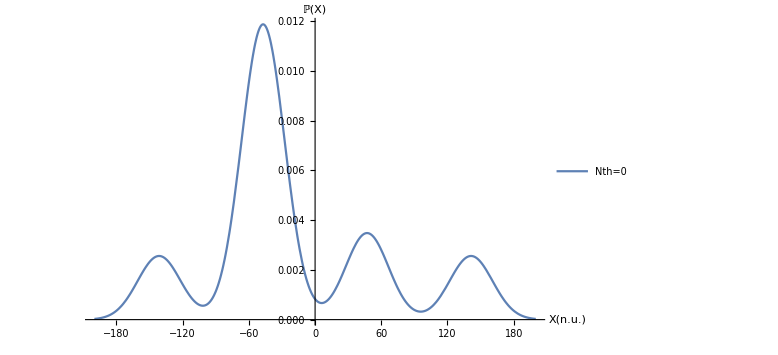

```mathematica
Plot[{P[x]},{x,-200,200},ImageSize->Large,PlotRange->All,AxesLabel->{"X(n.u.)","ℙ(X)"},PlotLegends->{"Nth=0","Nth=7.5","Nth=7500"},AxesStyle->Directive[Bold,FontSize->20]]
```

```mathematica
(*This last part was just the asymmetry plot for different temperatures for the parameter values specified in my thesis; I essentially just made a list for the maximal values of the distribution for the different temperatures and plot it; I didn't thought that this was of significant interest for later so I didn't build a code for it*)
```

```mathematica
data:=Import["D:\\jpereiramachad\\Desktop\\drafts of poetry\\Oferendas a Tjerk\\asymmetrytrend.dat"]
```

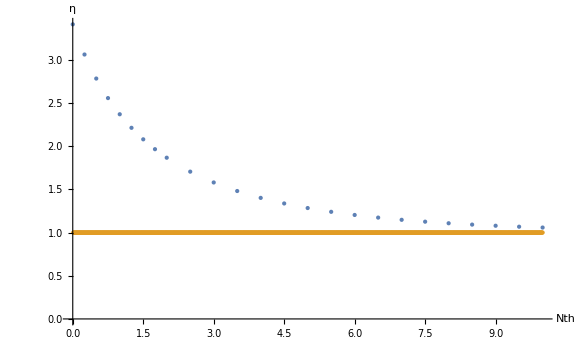

```mathematica
ListPlot[{data,Table[{0.01*n,1},{n,1000}]},ImageSize->Large,PlotRange->All,AxesLabel->{"Nth",η},PlotStyle->{PointSize[Large],PointSize[Small]},AxesStyle->Directive[Bold,FontSize->20]]
```